```mathematica
(* parameters *)
a=1000;  (* exp.norm *)
b=0.2 ; (* exp.slope *)
c=100 ; (* gauss norm *)
mu=8 ; (* peak location *)
sigma=1 ; (*  width *)
seed={a,b,c,mu,sigma};
```

```mathematica
model[x_, A_, B_, C_, D_,E_]:=A*Exp[-B*x]+C*Exp[-1/2*((x-D)/E)^2];
xobs= Range[19];
yobs={800,704,578,458,339,323,320,311,221,139,105,87,73,60,56,46,36,32,26};
ystd=Map[Sqrt[x],yobs];

Chi2[A_, B_, C_, D_,E_]:=Sum[Map[model[x, A, B, C, D,E],xobs],i]

obs=Transpose@{xobs,yobs};

p1=Plot[model[x,a,b,c,mu,sigma],{x,0,20}];
```

```mathematica
p2=ListPlot[obs,PlotRange->All,Frame->True,Axes->True];
```

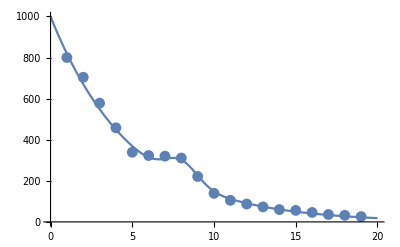

```mathematica
Show[p1,p2]
```

```mathematica
Chi2[a,b,c,mu,sigma]
```

Sum::itform: Argument {} at position 2 does not have the correct form for an iterator.

```mathematica
Sum[model[x,1000,0.2,100,8,1]/@xobs,{}]
```

Sum::itform: Argument {} at position 2 does not have the correct form for an iterator.

```mathematica
Map[model[x, a, b, c, mu,sigma],xobs]
```